```mathematica
(* Display the color slider *)
(*DynamicModule[{x},Column[{ColorSlider[Dynamic[x],ImageSize->{500,200}],Dynamic[x]}]]*)
ColorSlider[Dynamic[x],ImageSize->{500,200}]
```

$CellContext`x

```mathematica
(* run this line to get the RGB values *)
{x[[1]],x[[2]],x[[3]]}
```

{1.,0.911498,0.114946}

```mathematica
(* Test the tri-color scale below by substituting for c1, c2, and c3 *)

(* scale 1 *)
c1={1.0,0.5,0.0};
c2={0.0,0.88,1.0};
c3={0.9,0.0,0.9};

(* scale 2 *)
(*
c1={0.20689707789730677,1.,0.8731059739070726};
c2={1.,0.9114976729991607,0.11494621194781414};
c3={1.,0.39079880979629206,0.8903486686503395};
*)


(* print for easy copying into vmd proc *)
Print["set firstColor { ",NumberForm[c1[[1]],5]," ",NumberForm[c1[[2]],5]," ",NumberForm[c1[[3]],5]," }\nset middleColor { ",NumberForm[c2[[1]],5]," ",NumberForm[c2[[2]],5]," ",NumberForm[c2[[3]],5]," }\nset lastColor { ",NumberForm[c3[[1]],5]," ",NumberForm[c3[[2]],5]," ",NumberForm[c3[[3]],5]," }"]


(* color scaling function *)
func[val_,scaleMin_,scaleMax_]:=Module[{color1,color2,color3},
(*
color1={0.45517662317845425,0.,0.7586175326161593};
color2={0.22989242389562828,1.,0.2760967421988251};
color3={1.,0.39079880979629206,0.8903486686503395};
*)
color1=c1;
color2=c2;
color3=c3;

frac=(val-scaleMin)/(scaleMax-scaleMin);
If[frac<0.5,
Return[RGBColor[color1+2.0*frac*(color2-color1)]];
];
If[frac≥0.5,
Return[RGBColor[color2+2.0*(frac-0.5)*(color3-color2)]];
];

];
```

set firstColor { 1. 0.5 0. }
set middleColor { 0. 0.88 1. }
set lastColor { 0.9 0. 0.9 }

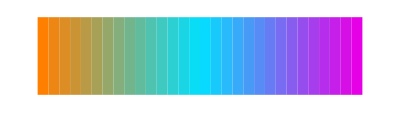

```mathematica
(* Plot the color scaling *)
n=30;

(* Array Plot Way *)
(*arr=Array[((#2-1)*1.0/n)&,{1,n+1}];
ArrayPlot[arr,ColorFunction->(func[#,0.0,1.0]&),ImageSize->500,ColorFunctionScaling->False,ImagePadding->0,PlotRangePadding->None]*)

(* PlotLegends Way *)
Needs["PlotLegends`"]
Graphics[Legend[func[#,0.0,1.0]&,n,LegendShadow->None,LegendBorder->None,LegendOrientation->Horizontal,LegendSize->{700,200}]]
```